## MODELAGEM DA DINÂMICA PLANA DE AERONAVE SUPERSÔNICA DE PASSAGEIROS DURANTE FASE DE FREE-ROLL DA ATERRISSAGEM

## PME3380 - Modelagem de Sistemas Dinâmicos Prof. Dr. Agenor de Toledo Fleury Prof. Dr. Renato Maia Matarazzo Orsino

## Grupo K Lucas Retore Carboni - 12676091 Roberto Tetsuo Hamaoka - 10334770 Vitor Lucas Buter - 12555700

## Modelo principal - toque e free-roll

O equacionamento é baseado no seguinte modelo físico:
-Graphics-

e  são definidos como variáveis incrementais a partir da posição de equilíbrio dinâmico do avião transladando em pista plana com velocidade constante (M.R.U)
Importando as funções necessárias ao código

```mathematica
SetDirectory @ NotebookDirectory[];
<<Linearize.m
```

As coordenadas generalizadas são definidas como:

```mathematica
𝕢[t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t]};
𝕧[t_] = {Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t]}; 
𝕦[t_] = {Subscript[y, ext][t], Subscript[y, ext]'[t]};
𝕪[t_] = { Subscript[q, 2][t], θ[t], Subscript[q, 2]'[t], θ'[t]};
Subscript[v, o] = {0, Subscript[q, 2]'[t], 0};
ω = {0, 0, 𝕧[t][[3]]};
```

Definindo os parâmetros físicos e geométricos do modelo

```mathematica
α = 𝕢[t][[3]] + Subscript[Φ, 0];
Subscript[ρ, PO] = {Subscript[D, PO]*Cos[(𝕢[t][[3]] + Subscript[Φ, 0])], Subscript[D, PO]*Sin[(𝕢[t][[3]] + Subscript[Φ, 0])], 0}; (*Vetor P-O*)
Subscript[ρ, GO] = {Subscript[D, GO]*Cos[(𝕢[t][[3]] + Subscript[Φ, 0])], Subscript[D, GO]*Sin[(𝕢[t][[3]] + Subscript[Φ, 0])], 0}; (*Vetor G-O*)
```

Definindo as forças e momentos externos do modelo

```mathematica
W = {0, -M*g, 0};
Subscript[D, ext] = {(-1/2)*Subscript[C, D]*S*ρ*(Subscript[u, longit]+Subscript[u, vento])^2, 0, 0};
Subscript[L, ext] = {0, (1/2)*Subscript[C, L]*S*ρ*(Subscript[u, longit]+Subscript[u, vento])^2, 0};
Subscript[F, rol] = {Subscript[μ, rol]*(W+Subscript[L, ext])[[2]], 0, 0};
Subscript[M, rol]= Cross[Subscript[ρ, GO], Subscript[F, rol]] //FullSimplify;
Subscript[M, aero] = Cross[Subscript[ρ, PO],(Subscript[L, ext]+Subscript[D, ext])] //FullSimplify;
Subscript[M, peso] = Cross[Subscript[ρ, GO], W] //FullSimplify;
Subscript[v, G]= Subscript[v, o] + Cross[ω , Subscript[ρ, GO]] //FullSimplify;
```

### Aplicação do TQMA

O momento angular do corpo do avião em relação a O é, já considerando o movimento como plano:

```mathematica
Subscript[H, o] = M*Cross[Subscript[ρ, GO], Subscript[v, o]] + ω*Subscript[J, oz] //FullSimplify;
D[Subscript[H, o], t] //FullSimplify;
M*Cross[Subscript[v, G], Subscript[v, o]] //FullSimplify;
TQMA = (D[Subscript[H, o], t] - M*Cross[Subscript[v, G], Subscript[v, o]]- Subscript[M, rol]- Subscript[M, aero] - Subscript[M, peso])[[3]]//FullSimplify;
```

### Aplicação do TMB no conjunto do trem de pouso (m) e no avião (M)

```mathematica
Subscript[a, G] = D[Subscript[v, o], t] + Cross[D[ω, t], Subscript[ρ, GO]] + Cross[ω, Cross[ω, Subscript[ρ, GO]]]
Subscript[TMB, m] = m*(D[𝕧[t][[1]], t]) + Subscript[k, r]*(𝕢[t][[1]] - 𝕦[t][[1]]) + Subscript[c, r]*(D[(𝕢[t][[1]] - 𝕦[t][[1]]), t]) - Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) - Subscript[c, t]*(D[(𝕢[t][[2]]-𝕢[t][[1]]), t]) //FullSimplify;
Subscript[TMB, M] = M*Subscript[a, G][[2]] + Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) + Subscript[c, t]*(D[(𝕢[t][[2]]-𝕢[t][[1]]), t]) - Subscript[L, ext][[2]]//FullSimplify;
```

{-Cos[Φ_0+θ[t]] D_GO θ'[t]^2-Sin[Φ_0+θ[t]] D_GO θ''[t],-Sin[Φ_0+θ[t]] D_GO θ'[t]^2+Cos[Φ_0+θ[t]] D_GO θ''[t]+q_2''[t],0}

### O espaço de estados

```mathematica
DIN = {Subscript[TMB, m], Subscript[TMB, M], TQMA};

Sol[t_] = Flatten @ Solve[
	(# == 0)& /@ DIN,
	𝕧'[t]
	] // Collect[#, 𝕧[t], FullSimplify]&;

𝕩[t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t]};
F = (𝕩'[t] /.Sol[t]); 
F //FullSimplify //MatrixForm
```

(q_1'[t]
q_2'[t]
θ'[t]
(k_t (-q_1[t]+q_2[t])+k_r (-q_1[t]+y_ext[t])+c_t (-q_1'[t]+q_2'[t])+c_r (-q_1'[t]+y_ext'[t]))/m
-(M Cos[Φ_0+θ[t]] D_GO^2 (2 g M Cos[Φ_0+θ[t]]+Sin[Φ_0+θ[t]] (-2 g M+S ρ C_L (u_longit+u_vento)^2) μ_rol)+1/2 M D_GO (-S ρ (Sin[2 (Φ_0+θ[t])] C_D+2 Cos[Φ_0+θ[t]]^2 C_L) D_PO (u_longit+u_vento)^2+4 Sin[Φ_0+θ[t]] J_oz θ'[t]^2)+J_oz (S ρ C_L (u_longit+u_vento)^2+2 k_t (q_1[t]-q_2[t])+2 c_t (q_1'[t]-q_2'[t])))/(2 M (M Cos[Φ_0+θ[t]]^2 D_GO^2-J_oz))
(Sec[Φ_0+θ[t]] (-S ρ D_PO (u_longit+u_vento)^2 (C_L+C_D Tan[Φ_0+θ[t]])+2 M Sin[Φ_0+θ[t]] D_GO^2 θ'[t]^2+D_GO (S ρ C_L (u_longit+u_vento)^2 (1+μ_rol Tan[Φ_0+θ[t]])+2 (g M-g M μ_rol Tan[Φ_0+θ[t]]+k_t (q_1[t]-q_2[t])+c_t (q_1'[t]-q_2'[t])))))/(2 M D_GO^2-2 Sec[Φ_0+θ[t]]^2 J_oz))

### Linearização

As variáveis são todas incrementais, assim  será linearizada em torno de 0, assim como   e  tomando  = 0 .

```mathematica
Subscript[q, 1eq] = (Subscript[L, ext][[2]])/Subscript[k, r];
Subscript[q, 2eq] = (Subscript[L, ext][[2]])/Subscript[k, t] + (Subscript[L, ext][[2]])/Subscript[k, r];
```

```mathematica
POSequi = {Subscript[q, 1][t] -> Subscript[q, 1eq] , Subscript[q, 2][t] -> Subscript[q, 2eq], θ[t] -> 0}; (*Posição de equilíbrio trivial do sistema*)
DINlin = Linearize[DIN, POSequi]; (*ELS -> Equação dinâmica não-linear*)

Sollin[t_] = Flatten @ Solve[
	(# == 0)& /@ DINlin,
	𝕧'[t]
	] // Collect[#, 𝕧[t], FullSimplify]&;
	
Subscript[𝕩, lin][t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t]};
Subscript[F, lin] = (Subscript[𝕩, lin]'[t] /.Sollin[t]);
Subscript[F, lin] //TrigReduce //FullSimplify //MatrixForm
```

(q_1'[t]
q_2'[t]
θ'[t]
(-(S ρ C_L (k_R-k_t) (u_longit+u_vento)^2)/k_R-2 (c_r+c_t) q_1'[t]+2 c_t q_2'[t]+2 (k_t (-q_1[t]+q_2[t])+k_r (-q_1[t]+y_ext[t])+c_r y_ext'[t]))/(2 m)
(M Cos[Φ_0] D_GO^2 k_R ((2 g M-S ρ C_L (u_longit+u_vento)^2) μ_rol (Sin[Φ_0]+Cos[Φ_0] θ[t])+2 g M (-Cos[Φ_0]+Sin[Φ_0] θ[t]))+M S ρ Cos[Φ_0] D_GO D_PO k_R (u_longit+u_vento)^2 (Cos[Φ_0] (C_L+C_D θ[t])+Sin[Φ_0] (C_D-C_L θ[t]))+J_oz (-S ρ C_L (k_R-k_t) (u_longit+u_vento)^2+2 k_R (k_t (-q_1[t]+q_2[t])+c_t (-q_1'[t]+q_2'[t]))))/(2 M (M Cos[Φ_0]^2 D_GO^2-J_oz) k_R)
(-S ρ D_PO k_R (u_longit+u_vento)^2 (Cos[Φ_0] (C_L+C_D θ[t])+Sin[Φ_0] (C_D-C_L θ[t]))+D_GO (-S ρ Cos[Φ_0] C_L k_t (u_longit+u_vento)^2+k_R (-2 g M Sin[Φ_0] (μ_rol+θ[t])+S ρ C_L (u_longit+u_vento)^2 (Cos[Φ_0]+μ_rol (Sin[Φ_0]+Cos[Φ_0] θ[t]))+2 Cos[Φ_0] (g M-g M μ_rol θ[t]+k_t (q_1[t]-q_2[t])+c_t (q_1'[t]-q_2'[t])))))/(2 (M Cos[Φ_0]^2 D_GO^2-J_oz) k_R))

```mathematica
𝔸 = CoefficientArrays[Subscript[F, lin], Subscript[𝕩, lin][t]][[2]]//Normal; 
𝔸 //FullSimplify//MatrixForm;

𝔹 = CoefficientArrays[Subscript[F, lin], 𝕦[t]][[2]]//Normal; 
𝔹 //MatrixForm;

ℂ = { {0,1,0,0,0,0}, {0,0,1,0,0,0}, {0,0,0,0,1,0}, {0,0,0,0,0,1}};
ℂ //MatrixForm;

𝔻 = {{0,0},{0,0},{0,0},{0,0}};
𝔻 //MatrixForm;

𝕩[t] //MatrixForm ;
𝕩'[t] //MatrixForm;
𝕦[t] //MatrixForm ;
𝕪[t] //MatrixForm ;
𝔸.𝕩[t] //MatrixForm;
```

### Substituindo os valores numéricos

```mathematica
rep = {Subscript[C, D] -> 0.00017*Subscript[Φ, 0]^2 + 0.01111*Subscript[Φ, 0] + 0.15714, Subscript[C, L] -> -0.00165*Subscript[Φ, 0]^2 + 0.07378*Subscript[Φ, 0] + 0.21999,  Subscript[k, t] -> 11486800, Subscript[c, t] -> 102196, Subscript[k, r]-> 13600000, Subscript[c, r] -> 9700, m -> 3000, M -> 88000, Subscript[D, GO] -> 2.2, Subscript[D, PO] -> 5, ρ -> 1.2923, S -> ((25.66/2)^2)/1.7, Subscript[J, oz] -> 16864415.983,  g -> 9.81, Subscript[μ, rol] -> (0.0041+0.000041*Subscript[u, longit])*Subscript[C, pav]};
SS = StateSpaceModel[{𝔸/.(rep)/.(Subscript[Φ, 0]->11*Pi/180)/.(Subscript[u, longit]->300/3.6)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), 𝔹/.(rep)/.(Subscript[Φ, 0]->11*Pi/180)/.(Subscript[u, longit]->300/3.6)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), ℂ, 𝔻}]
```

000100000000100000000100-125434/1557434/150-13987/37525549/750013600/397/30133.788-133.788-0.08103071.19029-1.19029000-1.507641.507640.0375215-0.01341320.013413200001000000001000000000100000000100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2461FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TF = TransferFunctionModel[SS, s]
```

```mathematica
(606504.1506786201+5395.958681508535 s)/(606496.5148656069+5828.504789524775 s+8499.902022017464 s^2+38.48895166994061 s^3+s^4)(432.58016629284253+3.848588177252168 s)/(606496.514865607+5828.504789524775 s+8499.902022017464 s^2+38.48895166994061 s^3+s^4)-(60.806392543647235 (4.786310984629252*^-13+1.0283090006039409*^-14 s+112.39970253238882 s^2+s^3))/(-22203.128260259513-213.37330579327403 s+606185.3472975508 s^2+5827.095771696436 s^3+8499.865413646303 s^4+38.48895166994061 s^5+s^6)-(0.0433692652704849 (6.553421934437634*^-13 s+112.3997025301501 s^2+s^3))/(-22203.128260259513-213.37330579327403 s+606185.3472975508 s^2+5827.095771696436 s^3+8499.865413646303 s^4+38.48895166994061 s^5+s^6)(606504.15067862 s+5395.958681508539 s^2)/(606496.5187720481+5828.504807213707 s+8499.902022477048 s^2+38.48895166994061 s^3+s^4)(432.5801662928398 s+3.848588177252168 s^2)/(606496.518772048+5828.504807213707 s+8499.902022477048 s^2+38.48895166994061 s^3+s^4)(-6834.620433973584 s^3-60.806392543647235 s^4)/(-22203.128260259513-213.37330579327403 s+606185.3472975508 s^2+5827.095771696436 s^3+8499.865413646303 s^4+38.48895166994061 s^5+s^6)(-4.874692515408241 s^3-0.04336926526957541 s^4)/(-22203.128260259513-213.37330579327403 s+606185.3472975508 s^2+5827.095771696436 s^3+8499.865413646303 s^4+38.48895166994061 s^5+s^6)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s24606504.1506786201432.58016629284253-60.806392543647235-0.0433692652704849606504.15067862432.5801662928398-6834.620433973584-4.874692515408241606496.5148656069606496.514865607-22203.128260259513-22203.128260259513606496.5187720481606496.518772048-22203.128260259513-22203.1282602595131FalseFalseFalseAutomaticNoneAutomatic
```

```mathematica
TransferFunctionPoles[TF] [[3]][[1]] //MatrixForm
TransferFunctionPoles[TF] [[4]][[1]] //MatrixForm
```

(-19.0614-89.7247 ⅈ
-19.0614+89.7247 ⅈ
-0.183061-8.4882 ⅈ
-0.183061+8.4882 ⅈ)

(-19.0614-89.7247 ⅈ
-19.0614+89.7247 ⅈ
-0.191334
-0.183061-8.4882 ⅈ
-0.183061+8.4882 ⅈ
0.191334)

```mathematica
TransferFunctionZeros[TF]
```

{{{-112.4},{-112.4}},{{-112.4,7.28847×10^-17-1.08214×10^-7 ⅈ,7.28847×10^-17+1.08214×10^-7 ⅈ},{-112.4,0,0}},{{-112.4,0},{-112.4,0}},{{-112.4,0,0,0},{-112.4,0,0,0}}}

### Diagrama de Bode

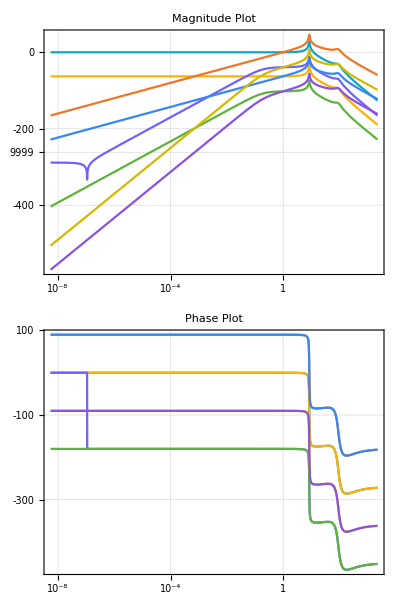

```mathematica
BodePlot[TF, PlotTheme->"Scientific", GridLines->Automatic, PlotStyle->100, PlotLabel->{"Magnitude Plot","Phase Plot"}]
```

## Pós toque

### Modelo incluindo trem de pouso frontal

-Graphics-

```mathematica
Subscript[𝕢, T][t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 3][t]};
Subscript[𝕧, T][t_] = {Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t], Subscript[q, 3]'[t]};
𝕦[t_] = {Subscript[y, ext][t], Subscript[y, ext]'[t]};
𝕪[t_] = {Subscript[q, 2][t], θ[t], Subscript[q, 2]'[t], θ'[t]};
Subscript[v, o] = {0, Subscript[q, 2]'[t], 0};
ω = {0, 0, Subscript[𝕧, T][t][[3]]};
```

Definindo os parâmetros físicos e geométricos do modelo

```mathematica
Subscript[ρ, PO] = {Subscript[D, PO]*Cos[(Subscript[𝕢, T][t][[3]])], Subscript[D, PO]*Sin[(Subscript[𝕢, T][t][[3]])], 0} (*Vetor P-O*);
Subscript[ρ, GO] = {Subscript[D, GO]*Cos[(Subscript[𝕢, T][t][[3]])], Subscript[D, GO]*Sin[(Subscript[𝕢, T][t][[3]])], 0} (*Vetor G-O*);
Subscript[ρ, FO] = {Subscript[D, FO]*Cos[(Subscript[𝕢, T][t][[3]])], Subscript[D, FO]*Sin[(Subscript[𝕢, T][t][[3]])], 0} (*Vetor G-O*);
```

Definindo as forças e momentos externos do modelo

```mathematica
W = {0, -M*g, 0};
Subscript[F, f] = {0, -Subscript[k, Tf]*(Subscript[D, FO]*Sin[θ[t]]+ Subscript[𝕢, T][t][[2]] - Subscript[𝕢, T][t][[4]]) - Subscript[c, Tf]*(D[(Subscript[D, FO]*Sin[θ[t]]+ Subscript[𝕢, T][t][[2]] - Subscript[𝕢, T][t][[4]]), t]), 0};
Subscript[D, ext] = {(-1/2)*Subscript[C, D]*S*ρ*(Subscript[u, longit]+Subscript[u, vento])^2, 0, 0};
Subscript[L, ext] = {0, (1/2)*Subscript[C, L]*S*ρ*(Subscript[u, longit]+Subscript[u, vento])^2, 0};
Subscript[F, rol] = {Subscript[μ, rol]*(W+Subscript[L, ext])[[2]], 0, 0};
Subscript[M, Tf] = Cross[Subscript[ρ, FO], Subscript[F, f]] //FullSimplify;
Subscript[M, rol]= Cross[Subscript[ρ, GO], Subscript[F, rol]] //FullSimplify;
Subscript[M, aero] = Cross[Subscript[ρ, PO],(Subscript[L, ext]+Subscript[D, ext])] //FullSimplify;
Subscript[M, peso] = Cross[Subscript[ρ, GO], W] //FullSimplify;
Subscript[v, G]= Subscript[v, o] + Cross[ω , Subscript[ρ, GO]] //FullSimplify;
```

### Aplicação do TQMA

O momento angular do corpo do avião em relação a O é, já considerando o movimento como plano:

```mathematica
Subscript[a, G] = D[Subscript[v, o], t] + Cross[D[ω, t], Subscript[ρ, GO]] + Cross[ω, Cross[ω, Subscript[ρ, GO]]];
Subscript[H, o] = M*Cross[Subscript[ρ, GO], Subscript[v, o]] + ω*Subscript[J, oz] //FullSimplify;
M*Cross[Subscript[v, G], Subscript[v, o]] //FullSimplify;
TQMA = (D[Subscript[H, o], t] - M*Cross[Subscript[v, G], Subscript[v, o]]- Subscript[M, rol]- Subscript[M, aero] - Subscript[M, peso] - Subscript[M, Tf])[[3]]//FullSimplify
```

-1/2 S ρ (Sin[θ[t]] C_D+Cos[θ[t]] C_L) D_PO (u_longit+u_vento)^2+Cos[θ[t]] D_FO^2 (Sin[θ[t]] k_Tf+Cos[θ[t]] c_Tf θ'[t])+Cos[θ[t]] D_FO (k_Tf (q_2[t]-q_3[t])+c_Tf (q_2'[t]-q_3'[t]))+J_oz θ''[t]+1/2 D_GO (Sin[θ[t]] (-2 g M+S ρ C_L (u_longit+u_vento)^2) μ_rol+2 M Cos[θ[t]] (g+q_2''[t]))

### Aplicação do TMB no conjunto do trem de pouso (m e mf) e no avião (M)

```mathematica
Subscript[a, G] = D[Subscript[v, o], t] + Cross[D[ω, t], Subscript[ρ, GO]] + Cross[ω, Cross[ω, Subscript[ρ, GO]]];
Subscript[TMB, m] = m*(D[Subscript[𝕧, T][t][[1]], t]) + Subscript[k, r]*(Subscript[𝕢, T][t][[1]] - 𝕦[t][[1]]) + Subscript[c, r]*(D[(Subscript[𝕢, T][t][[1]] - 𝕦[t][[1]]), t]) - Subscript[k, t]*(Subscript[𝕢, T][t][[2]]-Subscript[𝕢, T][t][[1]]) - Subscript[c, t]*(D[(Subscript[𝕢, T][t][[2]]-Subscript[𝕢, T][t][[1]]), t]) //FullSimplify;
Subscript[TMB, mf] = Subscript[m, f]*(D[Subscript[𝕧, T][t][[4]], t]) + Subscript[k, rf]*(Subscript[𝕢, T][t][[4]] - 𝕦[t][[1]]) + Subscript[c, rf]*(D[(Subscript[𝕢, T][t][[4]] - 𝕦[t][[1]]), t]) - Subscript[k, Tf]*(Subscript[D, FO]*Sin[θ[t]] + Subscript[q, 2][t] - Subscript[q, 3][t]) - Subscript[c, Tf]*(D[(Subscript[D, FO]*Sin[θ[t]]+ Subscript[q, 2][t] - Subscript[q, 3][t]), t]) //FullSimplify;
Subscript[TMB, M] = M*Subscript[a, G][[2]] + Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) + Subscript[c, t]*(D[(𝕢[t][[2]]-𝕢[t][[1]]), t]) + Subscript[k, Tf]*(Subscript[D, FO]*Sin[θ[t]] + Subscript[q, 2][t] - Subscript[q, 3][t]) + Subscript[c, Tf]*(D[(Subscript[D, FO]*Sin[θ[t]]+ Subscript[q, 2][t] - Subscript[q, 3][t]), t]) - Subscript[L, ext][[2]] + M*g //FullSimplify;
```

### O espaço de estados

```mathematica
DINf = {Subscript[TMB, m], Subscript[TMB, M], TQMA, Subscript[TMB, mf]};

Solf[t_] = Flatten @ Solve[
	(# == 0)& /@ DINf,
	Subscript[𝕧, T]'[t]
	] // Collect[#, Subscript[𝕧, T][t], FullSimplify]&;
	
𝕩f[t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 3][t], Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t], Subscript[q, 3]'[t]};
Ff = (𝕩f'[t] /.Solf[t]); 
Ff //FullSimplify //MatrixForm
```

(q_1'[t]
q_2'[t]
θ'[t]
q_3'[t]
(-g m+k_t (-q_1[t]+q_2[t])+k_r (-q_1[t]+y_ext[t])+c_t (-q_1'[t]+q_2'[t])+c_r (-q_1'[t]+y_ext'[t]))/m
(M Cos[θ[t]] D_GO^2 (-2 g M Cos[θ[t]]+Sin[θ[t]] (2 g M-S ρ C_L (u_longit+u_vento)^2) μ_rol)+J_oz (-S ρ C_L (u_longit+u_vento)^2+2 D_FO (Sin[θ[t]] k_Tf+Cos[θ[t]] c_Tf θ'[t])+2 (g M+k_t (-q_1[t]+q_2[t])+k_Tf (q_2[t]-q_3[t])+c_t (-q_1'[t]+q_2'[t])+c_Tf (q_2'[t]-q_3'[t])))+M D_GO (S ρ Cos[θ[t]] (Sin[θ[t]] C_D+Cos[θ[t]] C_L) D_PO (u_longit+u_vento)^2-2 Sin[θ[t]] J_oz θ'[t]^2-2 Cos[θ[t]]^2 D_FO^2 (Sin[θ[t]] k_Tf+Cos[θ[t]] c_Tf θ'[t])+2 Cos[θ[t]]^2 D_FO (k_Tf (-q_2[t]+q_3[t])+c_Tf (-q_2'[t]+q_3'[t]))))/(2 M (M Cos[θ[t]]^2 D_GO^2-J_oz))
(S ρ Sec[θ[t]] C_L (u_longit+u_vento)^2 (-D_PO+D_GO (1+μ_rol Tan[θ[t]]))+2 D_FO^2 (k_Tf Tan[θ[t]]+c_Tf θ'[t])-Sec[θ[t]] (S ρ C_D D_PO (u_longit+u_vento)^2 Tan[θ[t]]+2 D_GO (g M μ_rol Tan[θ[t]]+k_t (-q_1[t]+q_2[t])+k_Tf (q_2[t]-q_3[t])-M Sin[θ[t]] D_GO θ'[t]^2+c_t (-q_1'[t]+q_2'[t])+c_Tf (q_2'[t]-q_3'[t])))-2 Sec[θ[t]] D_FO (k_Tf (-q_2[t]+q_3[t])+D_GO (Sin[θ[t]] k_Tf+Cos[θ[t]] c_Tf θ'[t])+c_Tf (-q_2'[t]+q_3'[t])))/(2 M D_GO^2-2 Sec[θ[t]]^2 J_oz)
(-g m_f+k_Tf (q_2[t]-q_3[t])+k_rf (-q_3[t]+y_ext[t])+D_FO (Sin[θ[t]] k_Tf+Cos[θ[t]] c_Tf θ'[t])+c_Tf (q_2'[t]-q_3'[t])+c_rf (-q_3'[t]+y_ext'[t]))/m_f)

### Linearização

As variáveis são todas incrementais, assim  será linearizada em torno de 0, assim como   e  tomando  = 0 .

```mathematica
(*Subscript[m, eq]= Subscript[k, r]*(𝕢[t][[1]] - 𝕦[t][[1]]) - Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) + m*g;
Subscript[M, eq] = Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) - Subscript[L, ext][[2]] + M*g;
Subscript[q, 1eq] = SolveValues[Subscript[m, eq] == 0/.(Subscript[q, 2][t] -> SolveValues[Subscript[M, eq] == 0, 𝕢[t][[2]]]), 𝕢[t][[1]]];
Subscript[q, 2eq] = SolveValues[Subscript[M, eq] == 0/.(Subscript[q, 1][t] -> SolveValues[Subscript[m, eq] == 0, 𝕢[t][[1]]]), 𝕢[t][[2]]];*)
```

```mathematica
POSequif = {Subscript[q, 1][t] -> 0 , Subscript[q, 2][t] -> 0, θ[t] -> 0, Subscript[q, T1][t] -> 0}; (*Posição de equilíbrio trivial do sistema*)
DINflin = Linearize[DINf, POSequif]; (*ELS -> Equação dinâmica não-linear*)

Solflin[t_] = Flatten @ Solve[
	(# == 0)& /@ DINflin,
	Subscript[𝕧, T]'[t]
	] // Collect[#, Subscript[𝕧, T][t], FullSimplify]&;
	
Subscript[𝕩f, lin][t_] = {Subscript[q, 1][t], Subscript[q, 2][t], Subscript[θ, T][t], Subscript[q, T1][t], Subscript[q, 1]'[t], Subscript[q, 2]'[t], Subscript[θ, T]'[t], Subscript[q, T1]'[t]};
Subscript[Ff, lin] = (Subscript[𝕩f, lin]'[t] /.Solflin[t]);
Subscript[Ff, lin] //TrigReduce //FullSimplify //MatrixForm
```

(q_1'[t]
q_2'[t]
θ_T'[t]
q_T1'[t]
(-g m+k_t (-q_1[t]+q_2[t])+k_r (-q_1[t]+y_ext[t])+c_t (-q_1'[t]+q_2'[t])+c_r (-q_1'[t]+y_ext'[t]))/m
(M D_GO^2 (-2 g M+(2 g M-S ρ C_L (u_longit+u_vento)^2) μ_rol θ[t])+M D_GO (S ρ D_PO (u_longit+u_vento)^2 (C_L+C_D θ[t])-2 D_FO (k_Tf (q_2[t]-q_3[t])+D_FO (k_Tf θ[t]+c_Tf θ'[t])+c_Tf (q_2'[t]-q_3'[t])))+J_oz (-S ρ C_L (u_longit+u_vento)^2+2 (g M+k_t (-q_1[t]+q_2[t])+k_Tf (q_2[t]-q_3[t])+D_FO (k_Tf θ[t]+c_Tf θ'[t])+c_t (-q_1'[t]+q_2'[t])+c_Tf (q_2'[t]-q_3'[t]))))/(2 M (M D_GO^2-J_oz))
θ_T''[t]
q_T1''[t])

```mathematica
𝔸f = CoefficientArrays[Subscript[Ff, lin], Subscript[𝕩f, lin][t]][[2]]//Normal; 
𝔸f //FullSimplify//MatrixForm;

𝔹f = CoefficientArrays[Subscript[Ff, lin], 𝕦[t]][[2]]//Normal; 
𝔹f //MatrixForm;

ℂf = { {0,1,0,0,0,0,0,0}, {0,0,1,0,0,0,0,0}, {0,0,0,0,0,1,0,0}, {0,0,0,0,0,0,1,0}};
ℂf //MatrixForm;

𝔻f = {{0,0},{0,0},{0,0},{0,0}};
𝔻f //MatrixForm;
 
𝕩f[t] //MatrixForm ;
𝕩f'[t] //MatrixForm;
𝕦[t] //MatrixForm ;
𝕪[t] //MatrixForm ;
```

### Substituindo os valores numéricos

```mathematica
rep = {Subscript[C, D] -> 0.15714, Subscript[C, L] -> 0.21999,  Subscript[k, t] -> 11486800, Subscript[c, t] -> 102196, Subscript[k, r]-> 13600000, Subscript[c, r] -> 9700, Subscript[k, Tf] -> 5743400, Subscript[c, Tf] -> 51098, Subscript[k, rf]-> 3400000, Subscript[c, rf] -> 2425, m -> 3000, Subscript[m, f] -> 1500, M -> 88000, Subscript[D, GO] -> 2.2, Subscript[D, PO] -> 5, Subscript[D, FO] -> 32.5, ρ -> 1.2923, S -> ((25.6/2)^2)/1.7, Subscript[J, oz] -> 16864415.983,  g -> 9.81, Subscript[μ, rol] -> (0.0041+0.000041*Subscript[u, longit])*Subscript[C, pav]};
SS = StateSpaceModel[{𝔸f/.(rep)/.(Subscript[u, longit]->80)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), 𝔹f/.(rep)/.(Subscript[u, longit]->80)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), ℂf, 𝔻f}]
```

0000100000000001000000000010000000000100-125434/1557434/1500-13987/37525549/7500013600/397/30133.914-175.89001.19141-1.564860000000000000000000000000100000000001000000000000100000000001000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6$CellContext`stname7$CellContext`stname8Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2481FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TFf = TransferFunctionModel[SS, s]
```

(607076.+5401.05 s)/(958089.+10522.6 s+8555.94 s^2+38.8635 s^3+s^4)(432.988+3.85222 s)/(958089.+10522.6 s+8555.94 s^2+38.8635 s^3+s^4)0.0.(607076. s+5401.05 s^2)/(958089.+10522.6 s+8555.94 s^2+38.8635 s^3+s^4)(432.988 s+3.85222 s^2)/(958089.+10522.6 s+8555.94 s^2+38.8635 s^3+s^4)0.0.TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s24607076.2842359734432.988232138683030.0.607076.2842359737432.98823213889220.0.958088.7718401459958088.77184014591.1.958088.7718401459958088.77184014591.1.1FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TransferFunctionPoles[TFf] [[3]][[1]] //MatrixForm
TransferFunctionPoles[TFf] [[4]][[1]] //MatrixForm
```

(-19.0645-89.7252 ⅈ
-19.0645+89.7252 ⅈ
-0.367297-10.6646 ⅈ
-0.367297+10.6646 ⅈ)

{}

```mathematica
TransferFunctionZeros[TFf]
```

{{{-112.4},{-112.4}},{{},{}},{{-112.4,0},{-112.4,0}},{{},{}}}

### Diagrama de Bode

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

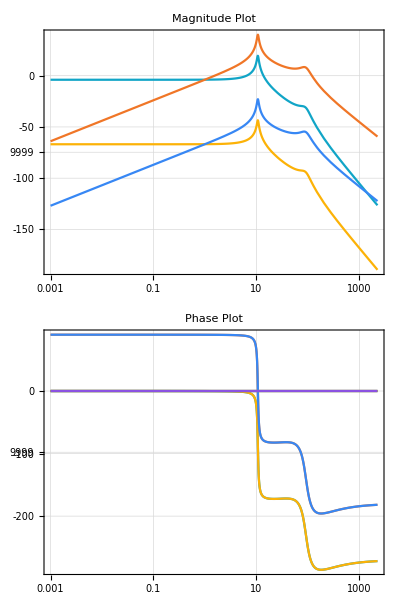

```mathematica
BodePlot[TFf, PlotTheme->"Scientific", GridLines->Automatic, PlotStyle->100, PlotLabel->{"Magnitude Plot","Phase Plot"}]
```

## Exportando o aquivo .m do espaço de estados

Para exportar outro espaço de estados, basta substituir o argumento da 4 linha da terceira célula de código por:
WriteString[fileD, (#/.(({ii_}→vv_):>(StringReplace[StringReplace[ToString @ StringForm[“    ``;”, (vv /. crule //CForm)], csqrule], csorule]<>”\n”)))]&/@ (Normal@(Select[#,Not @(NumericQ[#])&]&@Association@Delete[ArrayRules@SparseArray[(𝕩’[t]/.NOMEDASOLUCAO[t](*Join[𝕣𝕢[t], EOM2[t]]*))], -1]));

```mathematica
Unprotect[Power];
Format[Power[a_,n_Integer],CForm]:=Distribute[ConstantArray[Hold[a],n],Hold,List,HoldForm,Times]
Protect[Power];
```

```mathematica
crule = MapThread[#1->#2&, {#, x/@((Range[Length@#]))}& @ 𝕩[t]];
csorule = {"Cos"->"cos", "Sin"->"sin", "Tan"->"tan", "Sec"->"sec"};
csqrule = {};
```

```mathematica
fileD = OpenWrite["trab_esp_postoque.m"];
(*WriteString[fileD, (#/.(({ii_}->vv_):>(StringReplace[StringReplace[ToString @ StringForm["dy(``) = ``;", ii, (vv /. crule //CForm)], csqrule], csorule]<>"\n")))]&/@ (Normal@(Select[#,Not @(NumericQ[#])&]&@Association@Delete[ArrayRules@SparseArray[(𝕪'[t]/.EOM[t])], -1]));*)
WriteString[fileD, (#/.(({ii_}->vv_):>(StringReplace[StringReplace[ToString @ StringForm["    ``;", (vv /. crule //CForm)], csqrule], csorule]<>"\n")))]&/@ (Normal@(Select[#,Not @(NumericQ[#])&]&@Association@Delete[ArrayRules@SparseArray[(𝕩'[t]/.Sollin[t](*Join[𝕣𝕢[t], EOM2[t]]*))], -1]));
WriteString[fileD, "\n"];
Close[fileD];
```